#### Generar data aleatoria

```mathematica
data={};
While[Dimensions[data][[1]]<2^4,AppendTo[data,RandomInteger[{1,2^4}]];data=DeleteDuplicates[data];]
```

#### Introducir número a buscar

```mathematica
buscar=16;
```

#### Preparar el sistema y el oráculo

```mathematica
ket0={{1},{0}};
ket1={{0},{1}};
Id=IdentityMatrix[2];
H=HadamardMatrix[2];
ω=Position[data,buscar][[1,1]];
ketω=Table[{0},{2^4}];
ketω[[ω,1]]=1;
kets=KroneckerProduct[H,H,H,H].KroneckerProduct[ket0,ket0,ket0,ket0];
Uω=KroneckerProduct[Id,Id,Id,Id]-2ketω.ConjugateTranspose[ketω];
Us=2kets.ConjugateTranspose[kets]-KroneckerProduct[Id,Id,Id,Id];
G=Us.Uω;
```

#### Ejecutar el algoritmo

```mathematica
ketψ=KroneckerProduct[ket0,ket0,ket0,ket0];
ketψ=KroneckerProduct[H,H,H,H].ketψ;
Subscript[ketψ, 0]=ketψ;
For[i=1,i<2 π/4 √(Dimensions[ketψ][[1]])+1,i++,Subscript[ketψ, i]=G.Subscript[ketψ, i-1];]
```

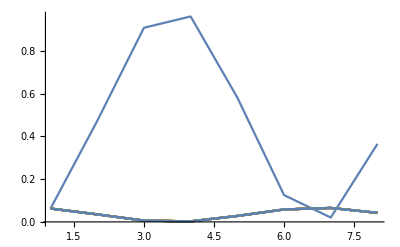

```mathematica
n=Floor[π/4 √(Dimensions[ketψ][[1]])];
Subscript[toplot, j_]:=Table[Abs[Subscript[ketψ, i][[j,1]]]^2,{i,0,2n+1}];
ListLinePlot[Table[Subscript[toplot, i],{i,1,16}],PlotRange->All]
```

#### Medir y probar resultado

```mathematica
RandomChoice[Flatten[Abs[Subscript[ketψ, n]]^2]->Table[i,{i,1,Dimensions[Subscript[ketψ, n]][[1]]}],20]
Position[data,buscar]
data[[Position[data,buscar][[1,1]]]]
```

{1,1,1,1,1,1,1,14,1,1,1,1,1,1,1,1,1,1,1,1}

{{1}}

16